# Fast Intro to Wolfram Language

## Interactive Usage

Evaluate simple inputs by typing into an input cell and pressing the ⇧+⌤ keys:

```mathematica
1+1
```

2

```mathematica
2*3
```

6

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
In[8]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Out[10]+In[8]
```

{3,4,5,6,7,8,9,10,11,12}

```mathematica
Out[5]+In[3]
```

{7,8,9,10,11,12,13,14,15,16}

## Built-in Functions

```mathematica
head[arg1,arg2,arg3,...]
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
FullForm[{1,2,3,4,5,6,7,8,9,10}]
```

List[1,2,3,4,5,6,7,8,9,10]

```mathematica
Range[3,6]
```

{3,4,5,6}

```mathematica
Range[17,36,5]
```

{17,22,27,32}

```mathematica
Range[30,60,5]
```

{30,35,40,45,50,55,60}

```mathematica
Nest[f,x,6]
```

f[f[f[f[f[f[x]]]]]]

```mathematica
Nest[f,x,10]
```

f[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]

```mathematica
Nest[f,x,1]
```

f[x]

```mathematica
Nest[f,x,2]
```

f[f[x]]

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
NestList[f,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

```mathematica
Framed[Framed[x]]
```

x

```mathematica
Nest[Framed[#,Background->RandomColor[]]&,x,7]
```

x

```mathematica
Nest[Framed[#,Background->RandomColor[]]&,"hello world",6]
```

hello world

```mathematica
Framed[Framed["hello world"]]
```

hello world

## Symbolic Expressions

```mathematica
{1,2,3}
```

```mathematica
List[1,2,3]
```

```mathematica
{1,2,3}==List[1,2,3]
```

True

```mathematica
2+2==Plus[2,2]
```

True

```mathematica
Plus[Power[x,2],Times[3,Power[y,3]]]
```

x^2+3 y^3

```mathematica
x^2+3 y^3
```

x^2+3 y^3

```mathematica
x^2+3 y^3
```

x^2+3 y^3

```mathematica
√25
```

5

```mathematica
√4
```

2

```mathematica
√-1
```

ⅈ

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
-Graphics3D-//EdgeDetect
```

-Graphics-

```mathematica
-Graphics3D-//EdgeDetect
```

-Graphics-

```mathematica
x
```

x

```mathematica
x=-Graphics3D-
```

-Graphics3D-

```mathematica
EdgeDetect[x]
```

-Graphics-

```mathematica
x^2
```

(-Graphics3D-)^2

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

```mathematica
FullForm[Hold[2+3]]
```

Hold[Plus[2,3]]

```mathematica
FullForm[2+3]
```

```mathematica
FullForm[5]
```

```mathematica
5
```

```mathematica
FullForm[Hold[2+3]]
```

Hold[Plus[2,3]]

```mathematica
Head[{1,2,3}]
```

List

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

```mathematica
Length[{1,2,3}]
```

3

## Lists

```mathematica
Clear[x]
```

```mathematica
{3,4,5.0786,7/8,x,y,x^2+3 x^3,{a,b,c},-Graphics3D-}
```

{3,4,5.0786,7/8,x,y,x^2+3 x^3,{a,b,c},-Graphics3D-}

```mathematica
Part[{a,b,c,d},3]
```

c

```mathematica
{a,b,c,d}[[3]]
```

c

```mathematica
{a,b,c,d}⟦3⟧
```

c

```mathematica
{a,b,c,d}⟦3⟧
```

c

```mathematica
Part[{a,b,c,d},1]
```

a

```mathematica
Part[{a,b,c,d},2]
```

b

```mathematica
Part[{a,b,c,d},3]
```

c

```mathematica
Part[{a,b,c,d},4]
```

d

```mathematica
Part[{a,b,c,d},5]
```

Part::partw: Part 5 of {a, b, c, d} does not exist.

{a,b,c,d}⟦5⟧

```mathematica
Part[{a,b,c,d},-1]
```

d

```mathematica
Last[{a,b,c,d}]
```

d

```mathematica
Part[{a,b,c,d},0]
```

List

```mathematica
Part[f[a,b,c,d],0]
```

f

```mathematica
Head[f[a,b,c]]
```

f

```mathematica
Part[{a,b,c,d},0]===Head[{a,b,c,d}]
```

True

```mathematica
{1,2,3}+2
```

{3,4,5}

```mathematica
{1,2,3}*3
```

{3,6,9}

```mathematica
{1,2,3}+27
```

{28,29,30}

```mathematica
{a,b,c}+{x,y,z}
```

{a+x,b+y,c+z}

```mathematica
{a,b,c}*{x,y,z}
```

{a x,b y,c z}

```mathematica
{a,b,c}.{x,y,z}
```

a x+b y+c z

```mathematica
Dot[{a,b,c},{x,y,z}]
```

a x+b y+c z

```mathematica
{a,b,c}+{x,y}
```

Thread::tdlen: Objects of unequal length in {a, b, c} + {x, y} cannot be combined.

{x,y}+{a,b,c}

```mathematica
Part[{1,2,3,4,5},3]
```

3

```mathematica
{1,2,3,4,5}[[3]]
```

3

```mathematica
rr=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
rr[[3;;7]]
```

{3,4,5,6,7}

```mathematica
rr[[2;;8]]
```

{2,3,4,5,6,7,8}

```mathematica
rr[[2;;8;;2]]
```

{2,4,6,8}

```mathematica
rr[[2;;8;;4]]
```

{2,6}

## Iterators

```mathematica
Do[..,{3}]
```

```mathematica
Table[x^2,{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
squares=Table[{x,x^2},{x,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
Grid[squares,Alignment->Right,Frame->All]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

```mathematica
list={};

For[x=1,x<11,x++,AppendTo[list,x^2]]

list
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
xxx=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
xxx[[3;;17;;4]]
```

{3,7,11,15}

```mathematica
Table[f[x],{x,4,20,2}]
```

{f[4],f[6],f[8],f[10],f[12],f[14],f[16],f[18],f[20]}

```mathematica
Table[f[x],{x,{74,356,346,224,775,345}}]
```

{f[74],f[356],f[346],f[224],f[775],f[345]}

```mathematica
Table[x^2,{x,{345423423,423423,423423423}}]
```

{119317341157036929,179287036929,179287395145036929}

```mathematica
Table[{i,j},{i,4},{j,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}}}

```mathematica
3 4
```

12

```mathematica
Table[i j,{i,4},{j,4}]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
Grid[Table[i j,{i,4},{j,4}],Background->Orange,Frame->All,ItemSize->4,Alignment->Right]
```

1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16

```mathematica
Grid[{{1,2},{3,4}}]
```

1 | 2
3 | 4

## Assignments

```mathematica
x=7
```

7

```mathematica
x
```

7

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
xxx=2232
```

2232

```mathematica
x123=534543
```

534543

```mathematica
x123
```

534543

```mathematica
DateString[]
```

Mon 21 Sep 2015 13:44:08

```mathematica
x=DateString[]
```

Wed 23 Sep 2015 15:42:59

```mathematica
x
```

Wed 23 Sep 2015 15:42:59

```mathematica
x
```

Wed 23 Sep 2015 15:42:59

```mathematica
xx
```

Mon 21 Sep 2015 13:44:09

```mathematica
xx
```

Mon 21 Sep 2015 13:44:09

```mathematica
date:=DateString[]
```

```mathematica
date
```

Wed 23 Sep 2015 15:43:43

```mathematica
date
```

Wed 23 Sep 2015 15:43:53

```mathematica
date
```

Wed 23 Sep 2015 15:44:05

```mathematica
ddd
```

Mon 21 Sep 2015 13:44:56

```mathematica
ddd
```

Mon 21 Sep 2015 13:45:05

```mathematica
ddd
```

Mon 21 Sep 2015 13:45:13

```mathematica
ddd
```

Mon 21 Sep 2015 13:45:55

```mathematica
Clear[ddd]
```

```mathematica
Clear[xxx]
```

```mathematica
xx=.
```

```mathematica
solvePlot
```

## Patterns

```mathematica
Clear[x]
```

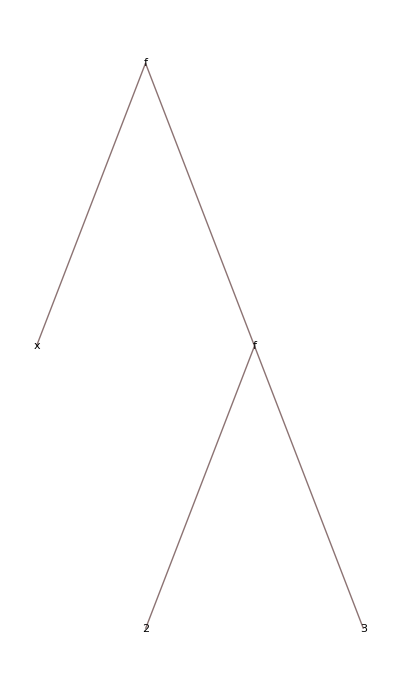

```mathematica
f[x,f[2,3]]//TreeForm
```

```mathematica
MatchQ[Sin[3],_]
```

True

```mathematica
MatchQ["xyz",_]
```

True

```mathematica
MatchQ[3.4,_]
```

True

```mathematica
MatchQ[2,_Integer]
```

True

```mathematica
MatchQ["xyz",_Integer]
```

False

```mathematica
MatchQ[3.4,_Integer]
```

False

```mathematica
MatchQ[3.4,_Real]
```

True

```mathematica
Cases[
{f[Sin[3]],g[2],f[5],g[3]},
f[_]]
```

{f[Sin[3]],f[5]}

```mathematica
Cases[{f[1],g[2],f[5],g[3]},g[_]]
```

{g[2],g[3]}

```mathematica
Cases[{f[1],g[2],f[5],g[3]},g[_Integer]]
```

{g[2],g[3]}

```mathematica
Cases[{f[1],g[2],f[5],g[3.5329483]},g[_Integer]]
```

{g[2]}

```mathematica
Cases[{f[1],g[2],f[5],g[3.9548375934]},g[_Real]]
```

{g[3.95484]}

```mathematica
Replace[f[100],f[_]->"hello world"]
```

hello world

```mathematica
Replace[f[100,123],f[_]->"hello world"]
```

f[100,123]

```mathematica
Replace[f[100,123],f[x_,y_]->"hello world"]
```

hello world

```mathematica
Replace[f[100,123],f[_,_]->"hello world"]
```

hello world

```mathematica
Clear[x]
```

```mathematica
Replace[f[100,123],f[x_,y_]->{x,y,"hello world"}]
```

{100,123,hello world}

```mathematica
Replace[f[100,123],f[x_,y_]->(x+y)]
```

223

```mathematica
Replace[f[2632,123],f[x_,y_]->x*y]
```

323736

```mathematica
Replace[f[534534543,534534534],f[x_,y_]->(x+y)]
```

1069069077

```mathematica
{f[1],g[2],f[5],g[3]}/.f[x_]->x+5
```

{6,g[2],10,g[3]}

## Function Definitions

```mathematica
f[x_,y_]:=x+y
```

```mathematica
f[2,3]
```

5

```mathematica
f[4,5]
```

9

```mathematica
f[5,6]
```

11

```mathematica
f[{1,3,4},{4,5,6}]
```

{5,8,10}

```mathematica
f[{1,2,3},3.4]
```

{4.4,5.4,6.4}

```mathematica
Clear[f]
```

```mathematica
f[1,2]
```

f[1,2]

```mathematica
f[1]=2
```

2

```mathematica
f[1]
```

2

```mathematica
f[1]
```

2

```mathematica
f[2]=3
```

3

```mathematica
f[3]
```

f[3]

```mathematica
{f[1],f[2],f[3],f[4]}
```

{2,3,f[3],f[4]}

```mathematica
f[{x_,y_},z_]:={x+z,y-z}
```

```mathematica
f[1,2]
```

f[1,2]

```mathematica
f[{10,20},3]
```

{13,17}

```mathematica
?f
```

Global`f

f[1]=2
 
f[2]=3
 
f[{x_,y_},z_]:={x+z,y-z}
 
f[u[x_]]:=x+1
 
f[v[x_]]:=x-1

```mathematica
f[u[x_]]:=x+1
```

```mathematica
f[v[x_]]:=x-1
```

```mathematica
f[1]
```

2

```mathematica
f[2]
```

3

```mathematica
f[3]
```

f[3]

```mathematica
f[v[34]]
```

33

## Pure Functions

```mathematica
(#+1)&
```

```mathematica
(#+1)&[3]
```

4

```mathematica
f[3]
```

```mathematica
3+1=4
```

```mathematica
(3#+7)&[5]
```

22

```mathematica
(#1*#2)&[4,5]
```

20

```mathematica
(#1^2+#2^2)&[4,5]
```

41

```mathematica
16+25
```

41

```mathematica
Clear[f]
```

```mathematica
f=(#1^2+#2^2)&
```

#1^2+#2^2&

```mathematica
f[4,5]
```

41

```mathematica
Clear[f]
```

```mathematica
f[x_,y_]:=x^2+y^2
```

```mathematica
f[4,5]
```

41

```mathematica
Function[{x,y},x^2+y^2]
```

Function[{x,y},x^2+y^2]

```mathematica
Function[{x,y},x^2+y^2][4,5]
```

41

```mathematica
Clear[f]
```

```mathematica
f=Function[{x,y},x^2+y^2]
```

Function[{x,y},x^2+y^2]

```mathematica
f[4,5]
```

41

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13},#>10&]
```

{11,12,13}

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13},#>6&]
```

{7,8,9,10,11,12,13}

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13},EvenQ[#]&]
```

{2,4,6,8,10,12}

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13},OddQ[#]&]
```

{1,3,5,7,9,11,13}

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13},PrimeQ[#]&]
```

{2,3,5,7,11,13}

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13},Not[PrimeQ[#]]&]
```

{1,4,6,8,9,10,12}

```mathematica
EvenQ[2]
```

True

```mathematica
EvenQ[3]
```

False

```mathematica
x
```

x

```mathematica
f[x]
f[f[x]]
f[f[f[x]]]
f[f[f[f[x]]]]
```

```mathematica
Clear[f]
```

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
NestList[f,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

```mathematica
Framed[x]
```

x

```mathematica
NestList[Framed,x,3]
```

{x,x,x,x}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

## Applying Functions

```mathematica
Apply[f,{1,2,3}]
```

f[1,2,3]

```mathematica
Apply[f,List[1,2,3]]
```

f[1,2,3]

```mathematica
Apply[f,g[1,2,3]]
```

f[1,2,3]

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Map[f,{g[1,2],2,3}]
```

{f[g[1,2]],f[2],f[3]}

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Map[#^2&,{1,2,3}]
```

{1,4,9}

```mathematica
Map[f,{{1,2},{3,4}}]
```

{f[{1,2}],f[{3,4}]}

```mathematica
Map[f,{{1,2},{3,4}},{2}]
```

{{f[1],f[2]},{f[3],f[4]}}

```mathematica
Map[f,{{1,2},{3,4}},2]
```

{f[{f[1],f[2]}],f[{f[3],f[4]}]}

```mathematica
Map[f,{{{1,2},{3,4}},{{5,6},{7,8}}}]
```

{f[{{1,2},{3,4}}],f[{{5,6},{7,8}}]}

```mathematica
Map[f,{{{1,2},{3,4}},{{5,6},{7,8}}},{2}]
```

{{f[{1,2}],f[{3,4}]},{f[{5,6}],f[{7,8}]}}

```mathematica
Map[f,{{{1,2},{3,4}},{{5,6},{7,8}}},{3}]
```

{{{f[1],f[2]},{f[3],f[4]}},{{f[5],f[6]},{f[7],f[8]}}}

```mathematica
Map[f,{{{1,2},{3,4}},{{5,6},{7,8}}},3]
```

{f[{f[{f[1],f[2]}],f[{f[3],f[4]}]}],f[{f[{f[5],f[6]}],f[{f[7],f[8]}]}]}

## Functionals & Operators

```mathematica
Nearest[{1,4,6,8,10,15},6.3]
```

{6}

```mathematica
Nearest[{1,4,6,8,10,15},7.9]
```

{8}

```mathematica
nearest=Nearest[{1,4,6,8,10,15}]
```

NearestFunction[{1, <>}]

```mathematica
nearest[6.3]
```

{6}

```mathematica
nearest[7.9]
```

{8}

```mathematica
Select[#>7&]
```

Select[#1>7&]

```mathematica
Select[#>7&][{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}]
```

{8,9,10,11,12,13,14,15}

```mathematica
Select[EvenQ[#]&][{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}]
```

{2,4,6,8,10,12,14}